```mathematica
A=-1.37*0.01;CC=1.34*10^(-4)*B;DD=1.19*10^(-8)B;x=(CC-DD)/A;c7=(2x-7-(81-28x+4x x)^(1/2))^2/32;c9=(2x-7+(81-28x+4x x)^(1/2))^2/32
```

1/32 (-7-0.0195603 B+√(81+0.273844 B+0.000382606 B^2))^2

```mathematica
{c7,c9}/.B->201.6
```

{16.9105,0.0591349}

```mathematica
c7
```

1/32 (-7-0.0195603 B-√(81+0.273844 B+0.000382606 B^2))^2

```mathematica
D[c7,B]/.B->201.6
```

0.0537016

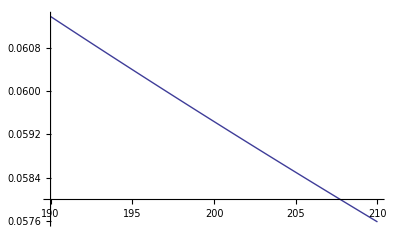

```mathematica
Plot[c9,{B,190,210}]
```

```mathematica
dc7=D[c7,B]
```

1/16 (-0.0195603-(0.273844+0.000765211 B)/(2 √(81+0.273844 B+0.000382606 B^2))) (-7-0.0195603 B-√(81+0.273844 B+0.000382606 B^2))

```mathematica
dc9=D[c9,B]
```

1/16 (-0.0195603+(0.273844+0.000765211 B)/(2 √(81+0.273844 B+0.000382606 B^2))) (-7-0.0195603 B+√(81+0.273844 B+0.000382606 B^2))

```mathematica
x/.B->201.6
```

-1.97168

```mathematica
CC/.B->201.6
```

0.0270144

```mathematica
DD/.B->201.6
```

2.39904×10^-6

```mathematica
x
```

-0.00978015 B

```mathematica
{c7,c9}/.B->201.6
```

{16.9105,0.0591349}

```mathematica
1/(1+c7)^2*dc7/.B->201.6
```

0.000167406

```mathematica
1/(1+c9)^2*dc9/.B->201.6
```

-0.000167406

```mathematica
1/((1+c7)(1+c9))^(1/2)(1/(1+c9)dc9+1/(1+c7)dc7)/.B->201.6
```

0.000647706

```mathematica
Ucc=(c7 as+at)/(1+c7);Uoo=(c9 as+at)/(1+c9);Uoc=Uco=(at-as)/((1+c7)(1+c9))^(1/2);U={{Ucc,Uco},{Uoc,Uoo}}
```

{{(at+1/32 as (-7-0.0195603 B-√(81+0.273844 B+0.000382606 B^2))^2)/(1+1/32 (-7-0.0195603 B-√(81+0.273844 B+0.000382606 B^2))^2),(-as+at)/(√((1+1/32 (-7-0.0195603 B-√(81+0.273844 B+0.000382606 B^2))^2) (1+1/32 (-7-0.0195603 B+√(81+0.273844 B+0.000382606 B^2))^2)))},{(-as+at)/(√((1+1/32 (-7-0.0195603 B-√(81+0.273844 B+0.000382606 B^2))^2) (1+1/32 (-7-0.0195603 B+√(81+0.273844 B+0.000382606 B^2))^2))),(at+1/32 as (-7-0.0195603 B+√(81+0.273844 B+0.000382606 B^2))^2)/(1+1/32 (-7-0.0195603 B+√(81+0.273844 B+0.000382606 B^2))^2)}}

```mathematica
U/.B->201.6
```

{{0.0558332 (16.9105 as+at),0.229599 (-as+at)},{0.229599 (-as+at),0.944167 (0.0591349 as+at)}}

```mathematica
D[Ucc,B]/.B->201.6
```

0.00299833 as-0.000167406 (16.9105 as+at)

```mathematica
Simplify[%]
```

{{-7.08387×10^-7 as+7.08387×10^-7 at,-7.91538×10^-7 as+7.91538×10^-7 at},{-7.91538×10^-7 as+7.91538×10^-7 at,7.08387×10^-7 as-7.08387×10^-7 at}}

```mathematica
D[U,{B,2}]/.B->201.6
```

{{-0.0000126876 as+7.08387×10^-7 (16.9105 as+at),7.91538×10^-7 (-as+at)},{7.91538×10^-7 (-as+at),7.50278×10^-7 as-7.08387×10^-7 (0.0591349 as+at)}}

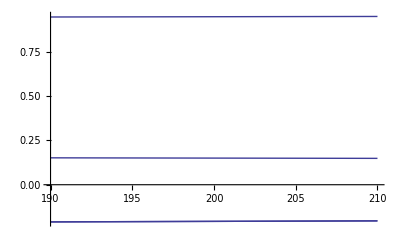

```mathematica
Plot[U/.{as->1,at->0.1},{B,190,210}]
```